reactions and transitions: (0→S | λ
S→0 | μ_s S
I1+S→2 I1 | β_1 i_1 S
I1+I2→2 I2 | β_2 i_1 i_2
I2+I3→2 I3 | β_3 i_2 i_3
I1→0 | i_1 μ_1
I2→0 | i_2 μ_2
I3→0 | i_3 μ_3)

(λ-β_1 i_1 S-μ_s S
-β_2 i_1 i_2-i_1 μ_1+β_1 i_1 S
β_2 i_1 i_2-β_3 i_2 i_3-i_2 μ_2
β_3 i_2 i_3-i_3 μ_3)

siphons are{{i_1},{i_2},{i_3}} edges={} E0 is{S→λ/μ_s,i_1→0,i_2→0,i_3→0} R1,R2, ... are{(β_1 λ)/(μ_1 μ_s)}

K=((β_1 S)/μ_1 | 0 | 0
0 | 0 | 0
0 | 0 | 0) F=(β_1 S | 0 | 0
0 | 0 | 0
0 | 0 | 0) V=(μ_1 | 0 | 0
0 | μ_2 | 0
0 | 0 | μ_3)

Minimal siphons: {T_1={i_1},T_2={i_2},T_3={i_3}}

IGMS edges: {1→2,2→3}

IGMS is acyclic (no cycles found)

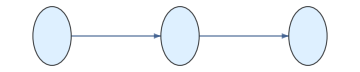

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];(*Get["HopfE`"];*)
(*Latex dictionary*)
Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];Format[be3]:=Subscript[β,3];
Format[mu1]:=Subscript[μ,1];Format[mu2]:=Subscript[μ,2];Format[mu3]:=Subscript[μ,3];
Format[muS]:=Subscript[μ,s];Format[m1]:=Subscript[m,1];Format[m2]:=Subscript[m,2];
Format[I1]:=Subscript[i,1];Format[I2]:=Subscript[i,2];
Format[I3]:=Subscript[i,3];Format[delta]:=δ;
Format[la]:=λ;
RN = {
 0 -> "S",
  "S" -> 0,
  "S" + "I1"   -> 2*"I1",
  "I1" + "I2"   -> 2*"I2",
  "I2" + "I3"  -> 2*"I3",
  "I1"         -> 0,
  "I2"         -> 0,
  "I3"        -> 0
};

rts = {
  la,            (* 0 -> S *)
  muS*S,          (* S -> 0 *)
  be1*S*I1,     (* S + I1 -> 2 I1 *)
  be2*I1*I2,     (* S + I2 -> 2 I2 *)
  be3*I2*I3,   (* S + I3 -> 2 I3 *)
 mu1*I1,         (* I1 -> 0 *)
  mu2*I2,         (* I2 -> 0 *)
  mu3*I3        (* I3 -> 0 *)
};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A,infV, gam,ng}= bdAn[RN,rts];
RHS//MatrixForm
Print["siphons are",mSi," edges=",edgIGMS[RN,mSI]," E0 is",E0," R1,R2, ... are",R0A/.E0]
jac=Grad[RHS,var];Print["K=",K//MatrixForm," F=",ng[[2]]//MatrixForm," V=",
ng[[3]]//MatrixForm]
{ed,cy,gr}=IGMS[RN,mSi];
```

```mathematica
Export["tree.pdf",gr]
```

tree.pdf